```mathematica
ρ[n_]:= Sqrt[1/2(-1+Sqrt[5-4n])]
```

```mathematica
g1[r_]:= r^6 + r^8/(2n)(1-Sqrt[1+(4n)/r^4-4n])
```

```mathematica
D[g1[r],r]
```

(4 r^3)/(√(1-4 n+(4 n)/r^4))+6 r^5+(4 (1-√(1-4 n+(4 n)/r^4)) r^7)/n

```mathematica
FullSimplify[(4 r^3)/(√(1-4 n+(4 n)/r^4))+6 r^5+(4 (1-√(1-4 n+(4 n)/r^4)) r^7)/n]
```

(4 r^3)/(√(1+4 n (-1+1/r^4)))+6 r^5-(4 (-1+√(1+4 n (-1+1/r^4))) r^7)/n

```mathematica
T1=Table[Solve[(4 r^3)/(√(1+4 n (-1+1/r^4)))+6 r^5-(4 (-1+√(1+4 n (-1+1/r^4))) r^7)/n==0,r][[i,1,2]],{i,1,8}]
```

Solve::nongen: 可能存在使某些解或所有解都无效的参数值.

General::stop: 在本次计算中，Solve::nongen 的进一步输出将被抑制.

{-√(-3/16-1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)-(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),√(-3/16-1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)-(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),-√(-3/16-1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)-(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),√(-3/16-1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)-(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),-√(-3/16+1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)+(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),√(-3/16+1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)+(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),-√(-3/16+1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)+(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))))),√(-3/16+1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)+(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)))))}

```mathematica
T1[[4]]
```

√(-3/16-1/2 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/2 √(9/32-(8-105 n+36 n^2)/(12 (-1+4 n))-(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))-1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)-(-27/64+(24 n)/(-1+4 n)+(3 (8-105 n+36 n^2))/(16 (-1+4 n)))/(4 √(9/64-(8-105 n+36 n^2)/(24 (-1+4 n))+(64-10320 n+53073 n^2-35208 n^3+1296 n^4)/(24 2^(2/3) (-1+4 n) (1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3))+1/(48 2^(1/3) (-1+4 n))(1024+389952 n-7015248 n^2+26891406 n^3-23932584 n^4+5155488 n^5+93312 n^6+√(1305870336 n+53292847104 n^2-176709040128 n^3-412839721728 n^4+758712220416 n^5-544755456000 n^6+1258475802624 n^7+4153623183360 n^8-8845153468416 n^9+1764644880384 n^10+1671768834048 n^11))^(1/3)))))

```mathematica
Plot[{ρ[n],T1[[4]]},{n,1/36,0.09},PlotTheme->"Detailed",PlotLegends->Placed[{"r_+","r_v"},{Left}],Frame->True,FrameLabel->{"n/无单位","{r_+,r_v}/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"}]
```

Placed::labpos: {Left} 不是标签放置的有效位置.

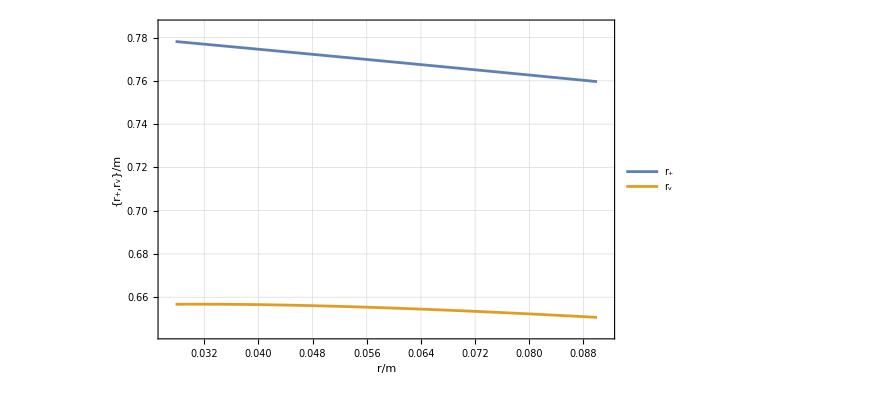

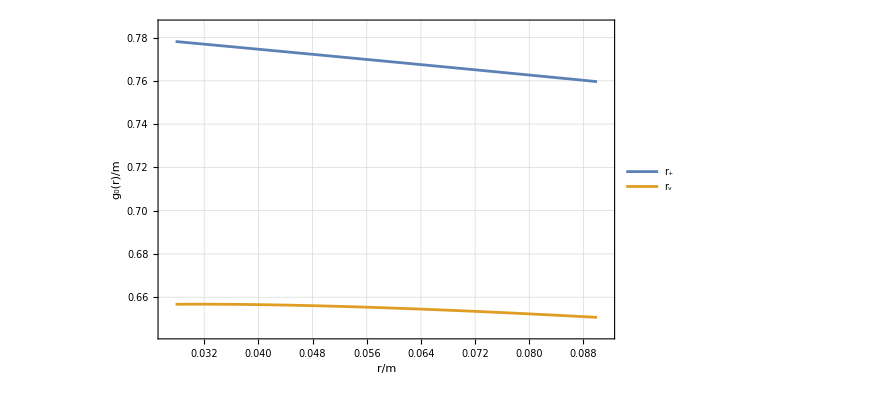

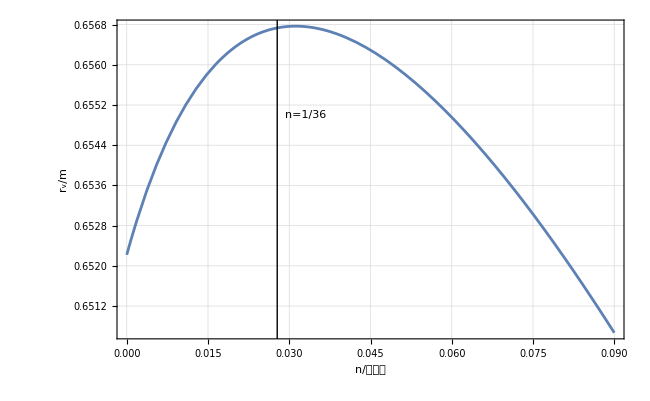

```mathematica
Plot[{T1[[4]]},{n,0,0.09},Epilog->{Line[{{1/36,0.6},{1/36,0.66}}],Inset["n=1/36",{0.033,0.655}]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"n/无单位","r_v/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotLegends->False,BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"}]
```

```mathematica
Vg1=Table[g1[r],{n,1/36,0.09,0.01}]
```

{r^6+18. (1-√(0.888889+0.111111/r^4)) r^8,r^6+13.2353 (1-√(0.848889+0.151111/r^4)) r^8,r^6+10.4651 (1-√(0.808889+0.191111/r^4)) r^8,r^6+8.65385 (1-√(0.768889+0.231111/r^4)) r^8,r^6+7.37705 (1-√(0.728889+0.271111/r^4)) r^8,r^6+6.42857 (1-√(0.688889+0.311111/r^4)) r^8,r^6+5.6962 (1-√(0.648889+0.351111/r^4)) r^8}

```mathematica
-g1[r]/.n->1/36
```

-r^6-18 (1-√(8/9+1/(9 r^4))) r^8

```mathematica
ρ[1/36]
```

√(1/2 (-1+(2 √11)/3))

```mathematica
N[{{r->-√(-1/2+(√11)/3)},{r->√(-1/2+(√11)/3)},{r->-ⅈ √(1/6 (3+2 √11))},{r->ⅈ √(1/6 (3+2 √11))}}]
```

{{r→-0.778166},{r→0.778166},{r→0.-1.2671 ⅈ},{r→0.+1.2671 ⅈ}}

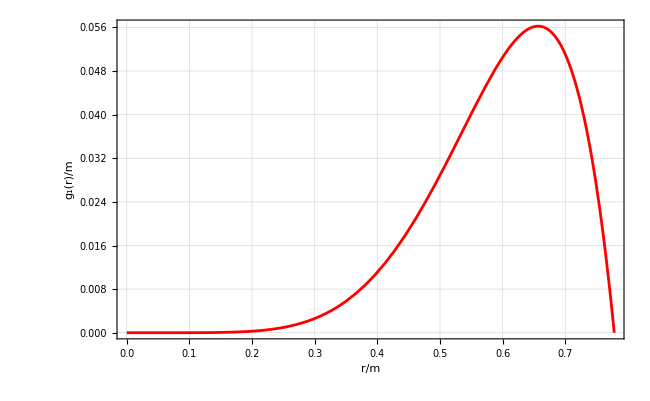

```mathematica
n1=Plot[-r^6-18 (1-√(8/9+1/(9 r^4))) r^8,{r,0,ρ[1/36]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,PlotRange->{0,All},FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Red]
```

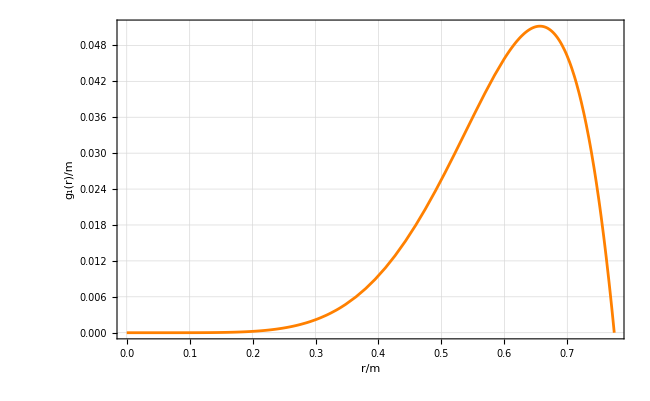

```mathematica
n2=Plot[-g1[r]/.n->0.04,{r,0,ρ[0.04]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Orange]
```

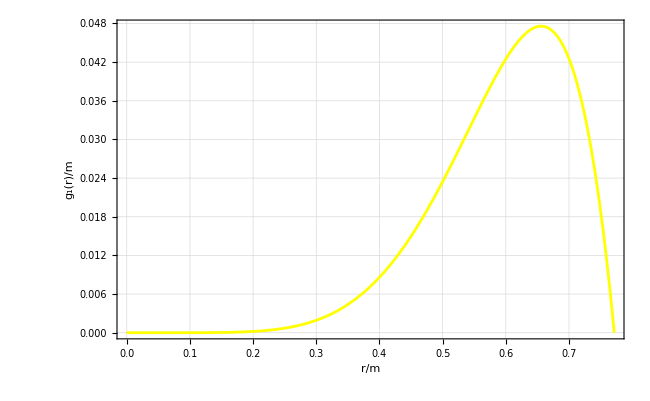

```mathematica
n3=Plot[-g1[r]/.n->0.05,{r,0,ρ[0.05]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Yellow]
```

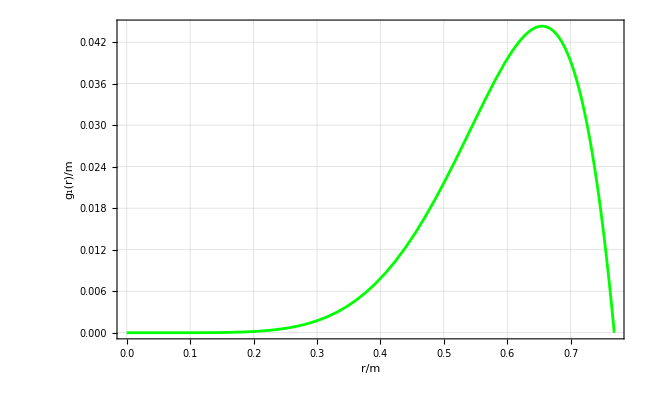

```mathematica
n4=Plot[-g1[r]/.n->0.06,{r,0,ρ[0.06]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Green]
```

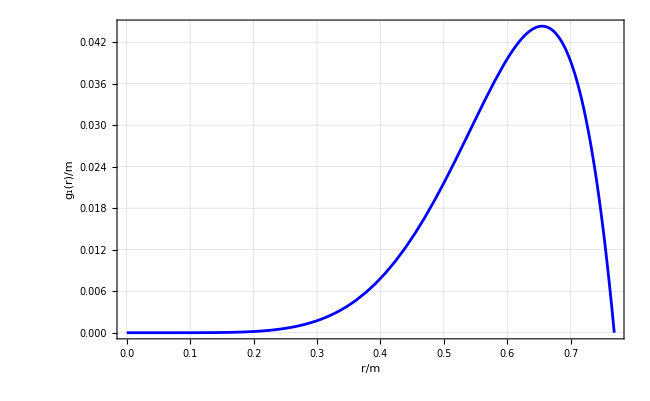

```mathematica
n5=Plot[-g1[r]/.n->0.06,{r,0,ρ[0.06]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Blue]
```

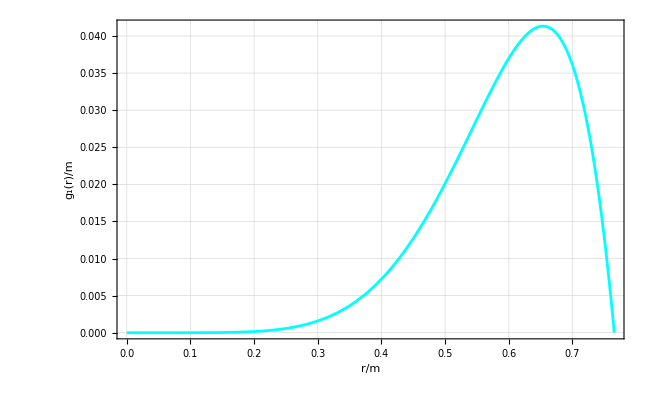

```mathematica
n6=Plot[-g1[r]/.n->0.07,{r,0,ρ[0.07]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Cyan]
```

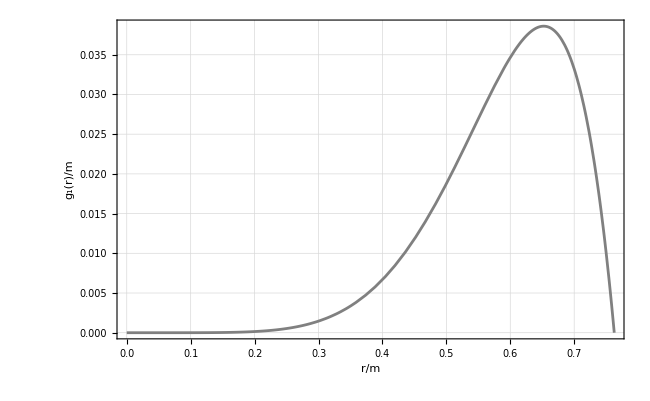

```mathematica
n7=Plot[-g1[r]/.n->0.08,{r,0,ρ[0.08]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Gray]
```

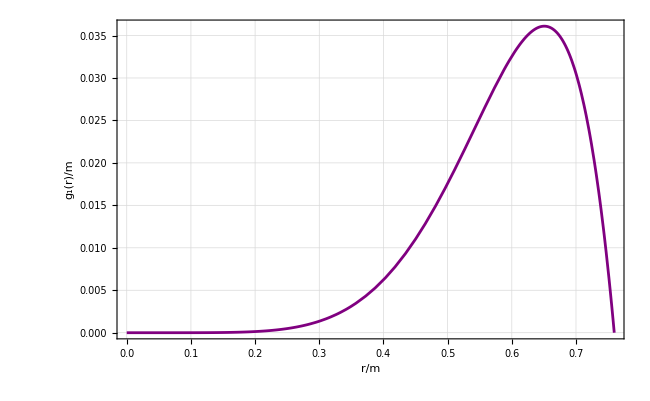

```mathematica
n8=Plot[-g1[r]/.n->0.09,{r,0,ρ[0.09]},PlotTheme->"Detailed",Frame->True,FrameLabel->{"r/m","g_1(r)/m"},ImageSize->650,FrameStyle->Directive[Black],LabelStyle->{FontFamily->"Times New Roman"},PlotRange->{0,All},BaseStyle->{FontSize->12 ,FontFamily->"Times New Roman"},PlotLegends->None,PlotStyle->Purple]
```

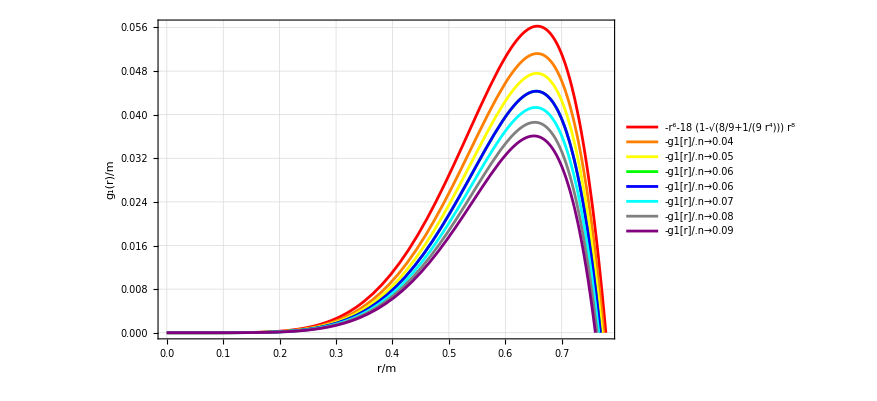

```mathematica
Show[n1,n2,n3,n4,n5,n6,n7,n8]
```